```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t11,t12,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t11(hop[a[1],a[4]])- t11(hop[a[2],a[5]])-t12(hop[a[1],a[5]]+hop[a[2],a[4]])
```

-t11 (a_(1↓)^†·a_(4↓)^+a_(1⇑)^†·a_(4⇑)^+a_(4↓)^†·a_(1↓)^+a_(4⇑)^†·a_(1⇑)^)-t12 (a_(1↓)^†·a_(5↓)^+a_(1⇑)^†·a_(5⇑)^+a_(2↓)^†·a_(4↓)^+a_(2⇑)^†·a_(4⇑)^+a_(4↓)^†·a_(2↓)^+a_(4⇑)^†·a_(2⇑)^+a_(5↓)^†·a_(1↓)^+a_(5⇑)^†·a_(1⇑)^)-t11 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t11 (a_(1↓)^†·a_(4↓)^+a_(1⇑)^†·a_(4⇑)^+a_(4↓)^†·a_(1↓)^+a_(4⇑)^†·a_(1⇑)^)-t12 (a_(1↓)^†·a_(5↓)^+a_(1⇑)^†·a_(5⇑)^+a_(2↓)^†·a_(4↓)^+a_(2⇑)^†·a_(4⇑)^+a_(4↓)^†·a_(2↓)^+a_(4⇑)^†·a_(2⇑)^+a_(5↓)^†·a_(1↓)^+a_(5⇑)^†·a_(1⇑)^)-t11 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->4,cj->U/5,U->6,t12->x t11,t11->0.3}
```

{Δ→4,𝒿→U/5,U→6,t12→t11 x,t11→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

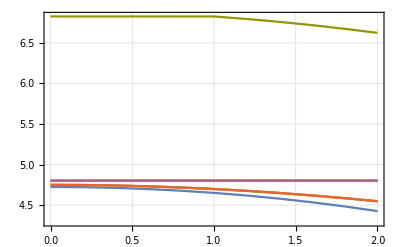

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic,PlotRange->All]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

-2.23115×10^-16

1

-2.24808×10^-16

1

-4.72587×10^-17

1

-1.90688×10^-16

1

-2.87349×10^-16

1

-6.32581×10^-17

1

1.27596×10^-16

1

1.27381×10^-16

1

1.637×10^-17

1

-1.40604×10^-16

1

-1.42614×10^-16

1

7.99181×10^-17

1

-6.40826×10^-17

1

-2.37724×10^-16

1

-2.96087×10^-17

1

2.75421×10^-17

1

-1.24862×10^-16

1

2.23194×10^-16

1

1.561×10^-16

1

3.19123×10^-17

1

-2.16323×10^-16

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

2

2.

$Aborted

```mathematica
data1//MatrixForm
```

(1 | 0. | -9.77787×10^-17 | 4.72319
1 | 0.1 | 4.78151×10^-17 | 4.72246
1 | 0.2 | 4.91841×10^-17 | 4.72027
1 | 0.3 | 7.92806×10^-17 | 4.71662
1 | 0.4 | 1.44255×10^-16 | 4.7115
1 | 0.5 | 4.57642×10^-17 | 4.70491
1 | 0.6 | 3.18583×10^-16 | 4.69685
1 | 0.7 | 6.43862×10^-17 | 4.68731
1 | 0.8 | 8.0437×10^-17 | 4.67628
1 | 0.9 | 1.60951×10^-16 | 4.66375
1 | 1. | 3.30761×10^-17 | 4.64972
1 | 1.1 | -6.14569×10^-17 | 4.63417
1 | 1.2 | 6.24885×10^-17 | 4.61709
1 | 1.3 | -3.15942×10^-16 | 4.59847
1 | 1.4 | 2.8314×10^-16 | 4.5783
1 | 1.5 | 1.24182×10^-16 | 4.55657
1 | 1.6 | 6.28948×10^-17 | 4.53327
1 | 1.7 | -1.42349×10^-17 | 4.50839
1 | 1.8 | -6.44973×10^-17 | 4.48191
1 | 1.9 | 6.10138×10^-17 | 4.45382
1 | 2. | -1.2468×10^-16 | 4.42412
2 | 0. | 2. | 4.74946
2 | 0.1 | 2. | 4.74893
2 | 0.2 | 2. | 4.74737
2 | 0.3 | 2. | 4.74475
2 | 0.4 | 2. | 4.7411
2 | 0.5 | 2. | 4.73641
2 | 0.6 | 2. | 4.73068
2 | 0.7 | 2. | 4.72393
2 | 0.8 | 2. | 4.71615
2 | 0.9 | 2. | 4.70736
2 | 1. | 2. | 4.69756
2 | 1.1 | 2. | 4.68675
2 | 1.2 | 2. | 4.67496
2 | 1.3 | 2. | 4.66219
2 | 1.4 | 2. | 4.64845
2 | 1.5 | 2. | 4.63376
2 | 1.6 | 2. | 4.61811
2 | 1.7 | 2. | 4.60153
2 | 1.8 | 2. | 4.58404
2 | 1.9 | 2. | 4.56563
2 | 2. | 2. | 4.54633
3 | 0. | 2. | 4.74946
3 | 0.1 | 2. | 4.74893
3 | 0.2 | 2. | 4.74737
3 | 0.3 | 2. | 4.74475
3 | 0.4 | 2. | 4.7411
3 | 0.5 | 2. | 4.73641
3 | 0.6 | 2. | 4.73068
3 | 0.7 | 2. | 4.72393
3 | 0.8 | 2. | 4.71615
3 | 0.9 | 2. | 4.70736
3 | 1. | 2. | 4.69756
3 | 1.1 | 2. | 4.68675
3 | 1.2 | 2. | 4.67496
3 | 1.3 | 2. | 4.66219
3 | 1.4 | 2. | 4.64845
3 | 1.5 | 2. | 4.63376
3 | 1.6 | 2. | 4.61811
3 | 1.7 | 2. | 4.60153
3 | 1.8 | 2. | 4.58404
3 | 1.9 | 2. | 4.56563
3 | 2. | 2. | 4.54633
4 | 0. | 2. | 4.74946
4 | 0.1 | 2. | 4.74893
4 | 0.2 | 2. | 4.74737
4 | 0.3 | 2. | 4.74475
4 | 0.4 | 2. | 4.7411
4 | 0.5 | 2. | 4.73641
4 | 0.6 | 2. | 4.73068
4 | 0.7 | 2. | 4.72393
4 | 0.8 | 2. | 4.71615
4 | 0.9 | 2. | 4.70736
4 | 1. | 2. | 4.69756
4 | 1.1 | 2. | 4.68675
4 | 1.2 | 2. | 4.67496
4 | 1.3 | 2. | 4.66219
4 | 1.4 | 2. | 4.64845
4 | 1.5 | 2. | 4.63376
4 | 1.6 | 2. | 4.61811
4 | 1.7 | 2. | 4.60153
4 | 1.8 | 2. | 4.58404
4 | 1.9 | 2. | 4.56563
4 | 2. | 2. | 4.54633
5 | 0. | 6. | 4.8
5 | 0.1 | 6. | 4.8
5 | 0.2 | 6. | 4.8
5 | 0.3 | 6. | 4.8
5 | 0.4 | 6. | 4.8
5 | 0.5 | 6. | 4.8
5 | 0.6 | 6. | 4.8
5 | 0.7 | 6. | 4.8
5 | 0.8 | 6. | 4.8
5 | 0.9 | 6. | 4.8
5 | 1. | 6. | 4.8
5 | 1.1 | 6. | 4.8
5 | 1.2 | 6. | 4.8
5 | 1.3 | 6. | 4.8
5 | 1.4 | 6. | 4.8
5 | 1.5 | 6. | 4.8
5 | 1.6 | 6. | 4.8
5 | 1.7 | 6. | 4.8
5 | 1.8 | 6. | 4.8
5 | 1.9 | 6. | 4.8
5 | 2. | 6. | 4.8
6 | 0. | 6. | 4.8
6 | 0.1 | 6. | 4.8
6 | 0.2 | 6. | 4.8
6 | 0.3 | 6. | 4.8
6 | 0.4 | 6. | 4.8
6 | 0.5 | 6. | 4.8
6 | 0.6 | 6. | 4.8
6 | 0.7 | 6. | 4.8
6 | 0.8 | 6. | 4.8
6 | 0.9 | 6. | 4.8
6 | 1. | 6. | 4.8
6 | 1.1 | 6. | 4.8
6 | 1.2 | 6. | 4.8
6 | 1.3 | 6. | 4.8
6 | 1.4 | 6. | 4.8
6 | 1.5 | 6. | 4.8
6 | 1.6 | 6. | 4.8
6 | 1.7 | 6. | 4.8
6 | 1.8 | 6. | 4.8
6 | 1.9 | 6. | 4.8
6 | 2. | 6. | 4.8
7 | 0. | 6. | 4.8
7 | 0.1 | 6. | 4.8
7 | 0.2 | 6. | 4.8
7 | 0.3 | 6. | 4.8
7 | 0.4 | 6. | 4.8
7 | 0.5 | 6. | 4.8
7 | 0.6 | 6. | 4.8
7 | 0.7 | 6. | 4.8
7 | 0.8 | 6. | 4.8
7 | 0.9 | 6. | 4.8
7 | 1. | 6. | 4.8
7 | 1.1 | 6. | 4.8
7 | 1.2 | 6. | 4.8
7 | 1.3 | 6. | 4.8
7 | 1.4 | 6. | 4.8
7 | 1.5 | 6. | 4.8
7 | 1.6 | 6. | 4.8
7 | 1.7 | 6. | 4.8
7 | 1.8 | 6. | 4.8
7 | 1.9 | 6. | 4.8
7 | 2. | 6. | 4.8
8 | 0. | 6. | 4.8
8 | 0.1 | 6. | 4.8
8 | 0.2 | 6. | 4.8
8 | 0.3 | 6. | 4.8
8 | 0.4 | 6. | 4.8
8 | 0.5 | 6. | 4.8
8 | 0.6 | 6. | 4.8
8 | 0.7 | 6. | 4.8
8 | 0.8 | 6. | 4.8
8 | 0.9 | 6. | 4.8
8 | 1. | 6. | 4.8
8 | 1.1 | 6. | 4.8
8 | 1.2 | 6. | 4.8
8 | 1.3 | 6. | 4.8
8 | 1.4 | 6. | 4.8
8 | 1.5 | 6. | 4.8
8 | 1.6 | 6. | 4.8
8 | 1.7 | 6. | 4.8
8 | 1.8 | 6. | 4.8
8 | 1.9 | 6. | 4.8
8 | 2. | 6. | 4.8
9 | 0. | 6. | 4.8
9 | 0.1 | 6. | 4.8
9 | 0.2 | 6. | 4.8
9 | 0.3 | 6. | 4.8
9 | 0.4 | 6. | 4.8
9 | 0.5 | 6. | 4.8
9 | 0.6 | 6. | 4.8
9 | 0.7 | 6. | 4.8
9 | 0.8 | 6. | 4.8
9 | 0.9 | 6. | 4.8
9 | 1. | 6. | 4.8
9 | 1.1 | 6. | 4.8
9 | 1.2 | 6. | 4.8
9 | 1.3 | 6. | 4.8
9 | 1.4 | 6. | 4.8
9 | 1.5 | 6. | 4.8
9 | 1.6 | 6. | 4.8
9 | 1.7 | 6. | 4.8
9 | 1.8 | 6. | 4.8
9 | 1.9 | 6. | 4.8
9 | 2. | 6. | 4.8
10 | 0. | 2. | 6.62676
10 | 0.1 | 2. | 6.62675
10 | 0.2 | 2. | 6.6267
10 | 0.3 | 2. | 6.62662
10 | 0.4 | 2. | 6.62651
10 | 0.5 | 2. | 6.62637
10 | 0.6 | 2. | 6.6262
10 | 0.7 | 2. | 6.62599
10 | 0.8 | 2. | 6.62576
10 | 0.9 | 2. | 6.62549
10 | 1. | 2. | 6.62519
10 | 1.1 | 2. | 6.61106
10 | 1.2 | 2. | 6.59567
10 | 1.3 | 2. | 6.57905
10 | 1.4 | 2. | 6.56121
10 | 1.5 | 2. | 6.54219
10 | 1.6 | 2. | 6.52199
10 | 1.7 | 0.75 | 6.50003
10 | 1.8 | 0.75 | 6.47663
10 | 1.9 | 0.75 | 6.45228
10 | 2. | 0.75 | 6.42698)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;21,1;;4]];
tmp03=Flatten[{tmp01},1];
e0data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[22;;42,1;;4]];
tmp03=Flatten[{tmp01},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 4.72319 | -9.77787×10^-17
0.1 | 4.72246 | 4.78151×10^-17
0.2 | 4.72027 | 4.91841×10^-17
0.3 | 4.71662 | 7.92806×10^-17
0.4 | 4.7115 | 1.44255×10^-16
0.5 | 4.70491 | 4.57642×10^-17
0.6 | 4.69685 | 3.18583×10^-16
0.7 | 4.68731 | 6.43862×10^-17
0.8 | 4.67628 | 8.0437×10^-17
0.9 | 4.66375 | 1.60951×10^-16
1. | 4.64972 | 3.30761×10^-17
1.1 | 4.63417 | -6.14569×10^-17
1.2 | 4.61709 | 6.24885×10^-17
1.3 | 4.59847 | -3.15942×10^-16
1.4 | 4.5783 | 2.8314×10^-16
1.5 | 4.55657 | 1.24182×10^-16
1.6 | 4.53327 | 6.28948×10^-17
1.7 | 4.50839 | -1.42349×10^-17
1.8 | 4.48191 | -6.44973×10^-17
1.9 | 4.45382 | 6.10138×10^-17
2. | 4.42412 | -1.2468×10^-16)

(0. | 4.74946 | 2.
0.1 | 4.74893 | 2.
0.2 | 4.74737 | 2.
0.3 | 4.74475 | 2.
0.4 | 4.7411 | 2.
0.5 | 4.73641 | 2.
0.6 | 4.73068 | 2.
0.7 | 4.72393 | 2.
0.8 | 4.71615 | 2.
0.9 | 4.70736 | 2.
1. | 4.69756 | 2.
1.1 | 4.68675 | 2.
1.2 | 4.67496 | 2.
1.3 | 4.66219 | 2.
1.4 | 4.64845 | 2.
1.5 | 4.63376 | 2.
1.6 | 4.61811 | 2.
1.7 | 4.60153 | 2.
1.8 | 4.58404 | 2.
1.9 | 4.56563 | 2.
2. | 4.54633 | 2.)

(0. | 4.8 | 6.
0.1 | 4.8 | 6.
0.2 | 4.8 | 6.
0.3 | 4.8 | 6.
0.4 | 4.8 | 6.
0.5 | 4.8 | 6.
0.6 | 4.8 | 6.
0.7 | 4.8 | 6.
0.8 | 4.8 | 6.
0.9 | 4.8 | 6.
1. | 4.8 | 6.
1.1 | 4.8 | 6.
1.2 | 4.8 | 6.
1.3 | 4.8 | 6.
1.4 | 4.8 | 6.
1.5 | 4.8 | 6.
1.6 | 4.8 | 6.
1.7 | 4.8 | 6.
1.8 | 4.8 | 6.
1.9 | 4.8 | 6.
2. | 4.8 | 6.)

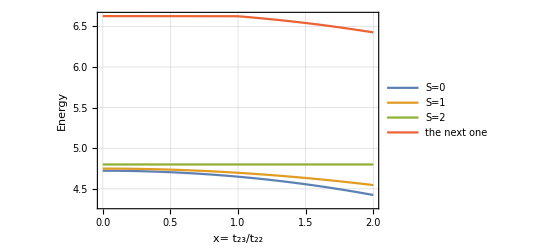

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

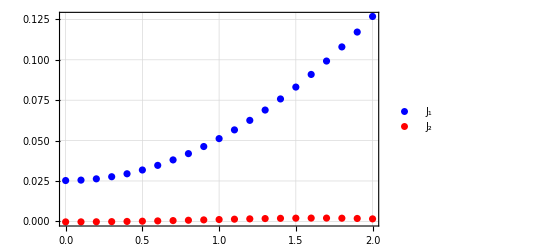

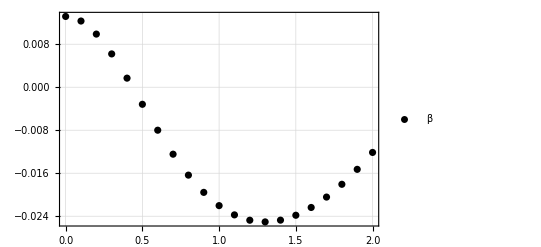

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J_1","J_2"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```